```mathematica
mathnum=1;
```

```mathematica
formnum=13;
```

```mathematica
<<NLOcompare.m
```

FeynCalc 9.0.1. For help, use the documentation center, check out the wiki or write to the mailing list.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

Package-X v1.0.4, by Hiren H. Patel

Contract::shdw: Symbol TraditionalForm`"Contract" appears in multiple contexts TraditionalForm`{"X`IndexAlg`", "FeynCalc`"}; definitions in context TraditionalForm`"X`IndexAlg`" may shadow or be shadowed by other definitions.

DiracMatrix::shdw: Symbol TraditionalForm`"DiracMatrix" appears in multiple contexts TraditionalForm`{"X`Spur`", "FeynCalc`"}; definitions in context TraditionalForm`"X`Spur`" may shadow or be shadowed by other definitions.

For more information, see the

```mathematica
<<renormAmpWest.res
```

```mathematica
Diagr=<<test/diagrBcnlo.m;
(* Amp =<<AmpBcnlo`; *)
AmpbeforeApart=<<test/AmpbeforeApartBcstarBcstar.m;
AmpafterFire=<<test/AmpafterFireBcstarBcstar.m;
```

```mathematica
Print[DateString[]];
```

Wed 10 Aug 2016 22:17:01

```mathematica
DiaMathRes[mathnum]
```

stage 1: Wed 10 Aug 2016 22:17:10

stage 2: Wed 10 Aug 2016 22:17:10

stage 3: Wed 10 Aug 2016 22:17:14

-(32 e pol1pol2 IntF(1/(OverBar[k1]^2-2 r (1)),k1) P1(mu) g_s^4)/(9 m^2 (-1+r)^4 r s (s/m^2-4)^2)+258+ϵ (-(16 e pol1pol2 s IntF(1/1,k1) P1(mu) g_s^4)/(27 m^6 (-1+r)^4 r (s/m^2-4)^2)+1/1+239+(8 e pol1P2 IntF(1) pol2(mu) g_s^4)/(9 m^2 (1)^2 r (1)^2))
 |  |  |  |

```mathematica
Print[DateString[]];
```

Wed 10 Aug 2016 22:17:18

```mathematica
tmp=DiaCompareCheck[mathnum,formnum,1.5,4.9,175,15^2]
```

stage 1: Wed 10 Aug 2016 22:17:32

stage 2: Wed 10 Aug 2016 22:17:32

stage 3: Wed 10 Aug 2016 22:17:36

stage 4: Wed 10 Aug 2016 22:17:36

stage 5: Wed 10 Aug 2016 22:17:52

stage 6: Wed 10 Aug 2016 22:17:53

stage 7: Wed 10 Aug 2016 22:18:01

mathres =

1.41032×10^-8 AA(5) eps pol1P2 pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]-0.0000123895 AA(9) eps pol1P2 C[174.516,2.25,131.891,1.5,1.5,0]-0.000024248 AA(5) eps pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]+0.0000123895 AA(7) eps pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]+4.07589×10^-6 AA(3) eps pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+4.05151×10^-7 AA(5) pol1P2 pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+2.47464×10^-6 AA(9) pol1P2 C[174.516,2.25,131.891,1.5,1.5,0]-5.4962×10^-6 AA(5) pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]-2.47464×10^-6 AA(7) pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]+6.44598×10^-6 AA(3) pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+1.79378×10^-10 AA(5) eps pol1P2 pol2P1 B(131.891,1.5,1.5)+9.22667×10^-11 AA(5) eps pol1P2 pol2P1 B(174.516,0,1.5)+5.42015×10^-7 AA(9) eps pol1P2 B(131.891,1.5,1.5)-6.2488×10^-7 AA(9) eps pol1P2 B(174.516,0,1.5)+8.51833×10^-7 AA(5) eps pol1pol2 B(131.891,1.5,1.5)-5.42015×10^-7 AA(7) eps pol1pol2 B(131.891,1.5,1.5)-9.68244×10^-7 AA(5) eps pol1pol2 B(174.516,0,1.5)+6.2488×10^-7 AA(7) eps pol1pol2 B(174.516,0,1.5)-1.80672×10^-7 AA(3) eps pol2P1 B(131.891,1.5,1.5)+2.08229×10^-7 AA(3) eps pol2P1 B(174.516,0,1.5)-1.73481×10^-8 AA(5) pol1P2 pol2P1 B(131.891,1.5,1.5)+1.9752×10^-8 AA(5) pol1P2 pol2P1 B(174.516,0,1.5)-1.40398×10^-7 AA(9) pol1P2 B(131.891,1.5,1.5)+1.61791×10^-7 AA(9) pol1P2 B(174.516,0,1.5)+2.43966×10^-7 AA(5) pol1pol2 B(131.891,1.5,1.5)+1.40398×10^-7 AA(7) pol1pol2 B(131.891,1.5,1.5)-2.79472×10^-7 AA(5) pol1pol2 B(174.516,0,1.5)-1.61791×10^-7 AA(7) pol1pol2 B(174.516,0,1.5)-2.20946×10^-7 AA(3) pol2P1 B(131.891,1.5,1.5)+2.54861×10^-7 AA(3) pol2P1 B(174.516,0,1.5)-1.12363×10^-9 A(1.5) AA(5) eps pol1P2 pol2P1+2.72778×10^-8 A(1.5) AA(9) eps pol1P2+8.08194×10^-8 A(1.5) AA(5) eps pol1pol2-2.72778×10^-8 A(1.5) AA(7) eps pol1pol2-2.72778×10^-8 A(1.5) AA(3) eps pol2P1-1.06841×10^-9 A(1.5) AA(5) pol1P2 pol2P1-6.16695×10^-9 A(1.5) AA(9) pol1P2+1.40055×10^-8 A(1.5) AA(5) pol1pol2+6.16695×10^-9 A(1.5) AA(7) pol1pol2-1.84142×10^-8 A(1.5) AA(3) pol2P1

formres =

-6.0023×10^-8 AA(5) eps pol1P2 pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+(AA(5) eps pol1P2 pol2P1 C[174.516,2.25,131.891,1.5,1.5,0])/(1366875 π^2)-0.0000123895 AA(9) eps pol1P2 C[174.516,2.25,131.891,1.5,1.5,0]-0.0000159088 AA(5) eps pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]-(AA(5) eps pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0])/(12150 π^2)+0.0000123895 AA(7) eps pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]+4.07589×10^-6 AA(3) eps pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+4.05151×10^-7 AA(5) pol1P2 pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+2.47464×10^-6 AA(9) pol1P2 C[174.516,2.25,131.891,1.5,1.5,0]-5.4962×10^-6 AA(5) pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]-2.47464×10^-6 AA(7) pol1pol2 C[174.516,2.25,131.891,1.5,1.5,0]+6.44598×10^-6 AA(3) pol2P1 C[174.516,2.25,131.891,1.5,1.5,0]+1.79378×10^-10 AA(5) eps pol1P2 pol2P1 B(131.891,1.5,1.5)+9.22667×10^-11 AA(5) eps pol1P2 pol2P1 B(174.516,0,1.5)+5.42015×10^-7 AA(9) eps pol1P2 B(131.891,1.5,1.5)-6.2488×10^-7 AA(9) eps pol1P2 B(174.516,0,1.5)+8.51833×10^-7 AA(5) eps pol1pol2 B(131.891,1.5,1.5)-5.42015×10^-7 AA(7) eps pol1pol2 B(131.891,1.5,1.5)-9.68244×10^-7 AA(5) eps pol1pol2 B(174.516,0,1.5)+6.2488×10^-7 AA(7) eps pol1pol2 B(174.516,0,1.5)-1.80672×10^-7 AA(3) eps pol2P1 B(131.891,1.5,1.5)+2.08229×10^-7 AA(3) eps pol2P1 B(174.516,0,1.5)-1.73481×10^-8 AA(5) pol1P2 pol2P1 B(131.891,1.5,1.5)+1.9752×10^-8 AA(5) pol1P2 pol2P1 B(174.516,0,1.5)-1.40398×10^-7 AA(9) pol1P2 B(131.891,1.5,1.5)+1.61791×10^-7 AA(9) pol1P2 B(174.516,0,1.5)+2.43966×10^-7 AA(5) pol1pol2 B(131.891,1.5,1.5)+1.40398×10^-7 AA(7) pol1pol2 B(131.891,1.5,1.5)-2.79472×10^-7 AA(5) pol1pol2 B(174.516,0,1.5)-1.61791×10^-7 AA(7) pol1pol2 B(174.516,0,1.5)-2.20946×10^-7 AA(3) pol2P1 B(131.891,1.5,1.5)+2.54861×10^-7 AA(3) pol2P1 B(174.516,0,1.5)-1.12363×10^-9 A(1.5) AA(5) eps pol1P2 pol2P1+2.72778×10^-8 A(1.5) AA(9) eps pol1P2+8.08194×10^-8 A(1.5) AA(5) eps pol1pol2-2.72778×10^-8 A(1.5) AA(7) eps pol1pol2-2.72778×10^-8 A(1.5) AA(3) eps pol2P1-1.06841×10^-9 A(1.5) AA(5) pol1P2 pol2P1-6.16695×10^-9 A(1.5) AA(9) pol1P2+1.40055×10^-8 A(1.5) AA(5) pol1pol2+6.16695×10^-9 A(1.5) AA(7) pol1pol2-1.84142×10^-8 A(1.5) AA(3) pol2P1

0

```mathematica
DiaCompare[mathnum,formnum,1.5,4.9,175,15^2]
```

stage 1: Wed 10 Aug 2016 22:18:04

stage 2: Wed 10 Aug 2016 22:18:04

stage 3: Wed 10 Aug 2016 22:18:08

stage 4: Wed 10 Aug 2016 22:18:08

stage 5: Wed 10 Aug 2016 22:18:14

stage 6: Wed 10 Aug 2016 22:18:15

stage 7: Wed 10 Aug 2016 22:18:16

0

```mathematica
dianumlist={{1,13},{2,14},{3,31},{4,32},{5,33},{6,34},{7,15},{8,16},{9,43},{10,44},{11,45},{12,46},{13,22},{14,23},{15,24},{16,25},{29,26},{30,27},{31,30},{32,28},{33,29},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,17},{43,18},{44,21},{45,19},{46,20},{47,48},{48,50},{49,47},{50,49},{51,57},{52,58},{53,59},{54,60},{55,61},{56,62},{57,63},{58,64},{59,65},{60,67},{61,68},{62,69},{63,70},{64,71},{65,72},{66,73},{67,74},{68,66},{69,88},{70,89},{71,90},{72,91},{73,92},{74,93},{75,94},{76,95},{77,87},{78,97},{79,98},{80,99},{81,100},{82,101},{83,102},{84,103},{85,104},{86,96}};
```

```mathematica
Print[DateString[]];
```

Wed 10 Aug 2016 22:18:16

```mathematica
DiaCompareList[dianumlist,1.5,4.9,175,15^2]
```

Checking diagrams with numbers 1 and 13

stage 1: Wed 10 Aug 2016 22:18:17

stage 2: Wed 10 Aug 2016 22:18:17

stage 3: Wed 10 Aug 2016 22:18:20

stage 4: Wed 10 Aug 2016 22:18:21

stage 5: Wed 10 Aug 2016 22:18:27

stage 6: Wed 10 Aug 2016 22:18:28

stage 7: Wed 10 Aug 2016 22:18:28

Checking diagrams with numbers 2 and 14

stage 1: Wed 10 Aug 2016 22:18:33

stage 2: Wed 10 Aug 2016 22:18:33

stage 3: Wed 10 Aug 2016 22:18:37

stage 4: Wed 10 Aug 2016 22:18:38

stage 5: Wed 10 Aug 2016 22:18:56

stage 6: Wed 10 Aug 2016 22:18:57

stage 7: Wed 10 Aug 2016 22:18:58

Checking diagrams with numbers 3 and 31

stage 1: Wed 10 Aug 2016 22:19:00

stage 2: Wed 10 Aug 2016 22:19:00

stage 3: Wed 10 Aug 2016 22:19:00

stage 4: Wed 10 Aug 2016 22:19:01

stage 5: Wed 10 Aug 2016 22:19:03

stage 6: Wed 10 Aug 2016 22:19:03

stage 7: Wed 10 Aug 2016 22:19:08

Checking diagrams with numbers 4 and 32

stage 1: Wed 10 Aug 2016 22:19:12

stage 2: Wed 10 Aug 2016 22:19:12

stage 3: Wed 10 Aug 2016 22:19:13

stage 4: Wed 10 Aug 2016 22:19:13

stage 5: Wed 10 Aug 2016 22:19:17

stage 6: Wed 10 Aug 2016 22:19:17

stage 7: Wed 10 Aug 2016 22:19:18

Checking diagrams with numbers 5 and 33

stage 1: Wed 10 Aug 2016 22:19:40

stage 2: Wed 10 Aug 2016 22:19:40

stage 3: Wed 10 Aug 2016 22:19:47

stage 4: Wed 10 Aug 2016 22:19:47

stage 5: Wed 10 Aug 2016 22:20:09

stage 6: Wed 10 Aug 2016 22:20:11

stage 7: Wed 10 Aug 2016 22:20:11

Checking diagrams with numbers 6 and 34

stage 1: Wed 10 Aug 2016 22:20:34

stage 2: Wed 10 Aug 2016 22:20:35

stage 3: Wed 10 Aug 2016 22:20:43

stage 4: Wed 10 Aug 2016 22:20:44

stage 5: Wed 10 Aug 2016 22:21:19

stage 6: Wed 10 Aug 2016 22:21:21

stage 7: Wed 10 Aug 2016 22:21:36

Checking diagrams with numbers 7 and 15

stage 1: Wed 10 Aug 2016 22:21:49

stage 2: Wed 10 Aug 2016 22:21:49

stage 3: Wed 10 Aug 2016 22:21:53

stage 4: Wed 10 Aug 2016 22:21:53

stage 5: Wed 10 Aug 2016 22:22:11

stage 6: Wed 10 Aug 2016 22:22:12

stage 7: Wed 10 Aug 2016 22:22:13

Checking diagrams with numbers 8 and 16

stage 1: Wed 10 Aug 2016 22:22:19

stage 2: Wed 10 Aug 2016 22:22:19

stage 3: Wed 10 Aug 2016 22:22:23

stage 4: Wed 10 Aug 2016 22:22:23

stage 5: Wed 10 Aug 2016 22:22:41

stage 6: Wed 10 Aug 2016 22:22:42

stage 7: Wed 10 Aug 2016 22:22:42

Checking diagrams with numbers 9 and 43

stage 1: Wed 10 Aug 2016 22:22:45

stage 2: Wed 10 Aug 2016 22:22:45

stage 3: Wed 10 Aug 2016 22:22:46

stage 4: Wed 10 Aug 2016 22:22:46

stage 5: Wed 10 Aug 2016 22:22:49

stage 6: Wed 10 Aug 2016 22:22:49

stage 7: Wed 10 Aug 2016 22:22:50

Checking diagrams with numbers 10 and 44

stage 1: Wed 10 Aug 2016 22:22:54

stage 2: Wed 10 Aug 2016 22:22:54

stage 3: Wed 10 Aug 2016 22:22:55

stage 4: Wed 10 Aug 2016 22:22:55

stage 5: Wed 10 Aug 2016 22:23:00

stage 6: Wed 10 Aug 2016 22:23:00

stage 7: Wed 10 Aug 2016 22:23:00

Checking diagrams with numbers 11 and 45

stage 1: Wed 10 Aug 2016 22:23:25

stage 2: Wed 10 Aug 2016 22:23:25

stage 3: Wed 10 Aug 2016 22:23:34

stage 4: Wed 10 Aug 2016 22:23:34

stage 5: Wed 10 Aug 2016 22:24:12

stage 6: Wed 10 Aug 2016 22:24:14

stage 7: Wed 10 Aug 2016 22:24:22

Checking diagrams with numbers 12 and 46

stage 1: Wed 10 Aug 2016 22:24:47

stage 2: Wed 10 Aug 2016 22:24:47

stage 3: Wed 10 Aug 2016 22:24:54

stage 4: Wed 10 Aug 2016 22:24:54

stage 5: Wed 10 Aug 2016 22:25:18

stage 6: Wed 10 Aug 2016 22:25:19

stage 7: Wed 10 Aug 2016 22:25:20

Checking diagrams with numbers 13 and 22

stage 1: Wed 10 Aug 2016 22:25:29

stage 2: Wed 10 Aug 2016 22:25:29

stage 3: Wed 10 Aug 2016 22:25:33

stage 4: Wed 10 Aug 2016 22:25:33

stage 5: Wed 10 Aug 2016 22:25:52

stage 6: Wed 10 Aug 2016 22:25:53

stage 7: Wed 10 Aug 2016 22:26:01

Checking diagrams with numbers 14 and 23

stage 1: Wed 10 Aug 2016 22:26:06

stage 2: Wed 10 Aug 2016 22:26:06

stage 3: Wed 10 Aug 2016 22:26:10

stage 4: Wed 10 Aug 2016 22:26:10

stage 5: Wed 10 Aug 2016 22:26:28

stage 6: Wed 10 Aug 2016 22:26:29

stage 7: Wed 10 Aug 2016 22:26:30

Checking diagrams with numbers 15 and 24

stage 1: Wed 10 Aug 2016 22:26:39

stage 2: Wed 10 Aug 2016 22:26:39

stage 3: Wed 10 Aug 2016 22:26:43

stage 4: Wed 10 Aug 2016 22:26:43

stage 5: Wed 10 Aug 2016 22:27:03

stage 6: Wed 10 Aug 2016 22:27:04

stage 7: Wed 10 Aug 2016 22:27:05

Checking diagrams with numbers 16 and 25

stage 1: Wed 10 Aug 2016 22:27:10

stage 2: Wed 10 Aug 2016 22:27:11

stage 3: Wed 10 Aug 2016 22:27:14

stage 4: Wed 10 Aug 2016 22:27:14

stage 5: Wed 10 Aug 2016 22:27:33

stage 6: Wed 10 Aug 2016 22:27:35

stage 7: Wed 10 Aug 2016 22:27:35

Checking diagrams with numbers 29 and 26

stage 1: Wed 10 Aug 2016 22:27:48

stage 2: Wed 10 Aug 2016 22:27:48

stage 3: Wed 10 Aug 2016 22:27:53

stage 4: Wed 10 Aug 2016 22:27:53

stage 5: Wed 10 Aug 2016 22:28:22

stage 6: Wed 10 Aug 2016 22:28:23

stage 7: Wed 10 Aug 2016 22:28:31

Checking diagrams with numbers 30 and 27

stage 1: Wed 10 Aug 2016 22:28:44

stage 2: Wed 10 Aug 2016 22:28:44

stage 3: Wed 10 Aug 2016 22:28:49

stage 4: Wed 10 Aug 2016 22:28:49

stage 5: Wed 10 Aug 2016 22:29:20

stage 6: Wed 10 Aug 2016 22:29:21

stage 7: Wed 10 Aug 2016 22:29:22

Checking diagrams with numbers 31 and 30

stage 1: Wed 10 Aug 2016 22:30:15

stage 2: Wed 10 Aug 2016 22:30:17

stage 3: Wed 10 Aug 2016 22:30:52

stage 4: Wed 10 Aug 2016 22:30:54

stage 5: Wed 10 Aug 2016 22:33:10

stage 6: Wed 10 Aug 2016 22:33:13

stage 7: Wed 10 Aug 2016 22:33:14

Checking diagrams with numbers 32 and 28

stage 1: Wed 10 Aug 2016 22:34:29

stage 2: Wed 10 Aug 2016 22:34:30

stage 3: Wed 10 Aug 2016 22:34:49

stage 4: Wed 10 Aug 2016 22:34:50

stage 5: Wed 10 Aug 2016 22:36:14

stage 6: Wed 10 Aug 2016 22:36:16

stage 7: Wed 10 Aug 2016 22:36:18

Checking diagrams with numbers 33 and 29

stage 1: Wed 10 Aug 2016 22:38:13

stage 2: Wed 10 Aug 2016 22:38:14

stage 3: Wed 10 Aug 2016 22:38:34

stage 4: Wed 10 Aug 2016 22:38:35

stage 5: Wed 10 Aug 2016 22:40:07

stage 6: Wed 10 Aug 2016 22:40:09

stage 7: Wed 10 Aug 2016 22:40:11

Checking diagrams with numbers 34 and 35

stage 1: Wed 10 Aug 2016 22:40:16

stage 2: Wed 10 Aug 2016 22:40:16

stage 3: Wed 10 Aug 2016 22:40:16

stage 4: Wed 10 Aug 2016 22:40:16

stage 5: Wed 10 Aug 2016 22:40:18

stage 6: Wed 10 Aug 2016 22:40:19

stage 7: Wed 10 Aug 2016 22:40:24

Checking diagrams with numbers 35 and 36

stage 1: Wed 10 Aug 2016 22:40:28

stage 2: Wed 10 Aug 2016 22:40:28

stage 3: Wed 10 Aug 2016 22:40:29

stage 4: Wed 10 Aug 2016 22:40:29

stage 5: Wed 10 Aug 2016 22:40:32

stage 6: Wed 10 Aug 2016 22:40:33

stage 7: Wed 10 Aug 2016 22:40:33

Checking diagrams with numbers 36 and 37

stage 1: Wed 10 Aug 2016 22:40:50

stage 2: Wed 10 Aug 2016 22:40:50

stage 3: Wed 10 Aug 2016 22:40:55

stage 4: Wed 10 Aug 2016 22:40:55

stage 5: Wed 10 Aug 2016 22:41:20

stage 6: Wed 10 Aug 2016 22:41:21

stage 7: Wed 10 Aug 2016 22:41:22

Checking diagrams with numbers 37 and 38

stage 1: Wed 10 Aug 2016 22:41:41

stage 2: Wed 10 Aug 2016 22:41:42

stage 3: Wed 10 Aug 2016 22:41:49

stage 4: Wed 10 Aug 2016 22:41:50

stage 5: Wed 10 Aug 2016 22:42:27

stage 6: Wed 10 Aug 2016 22:42:30

stage 7: Wed 10 Aug 2016 22:42:38

Checking diagrams with numbers 38 and 39

stage 1: Wed 10 Aug 2016 22:42:44

stage 2: Wed 10 Aug 2016 22:42:44

stage 3: Wed 10 Aug 2016 22:42:45

stage 4: Wed 10 Aug 2016 22:42:45

stage 5: Wed 10 Aug 2016 22:42:47

stage 6: Wed 10 Aug 2016 22:42:48

stage 7: Wed 10 Aug 2016 22:42:53

Checking diagrams with numbers 39 and 40

stage 1: Wed 10 Aug 2016 22:42:58

stage 2: Wed 10 Aug 2016 22:42:58

stage 3: Wed 10 Aug 2016 22:42:58

stage 4: Wed 10 Aug 2016 22:42:59

stage 5: Wed 10 Aug 2016 22:43:01

stage 6: Wed 10 Aug 2016 22:43:02

stage 7: Wed 10 Aug 2016 22:43:02

Checking diagrams with numbers 40 and 41

stage 1: Wed 10 Aug 2016 22:43:22

stage 2: Wed 10 Aug 2016 22:43:23

stage 3: Wed 10 Aug 2016 22:43:31

stage 4: Wed 10 Aug 2016 22:43:31

stage 5: Wed 10 Aug 2016 22:44:09

stage 6: Wed 10 Aug 2016 22:44:11

stage 7: Wed 10 Aug 2016 22:44:20

Checking diagrams with numbers 41 and 42

stage 1: Wed 10 Aug 2016 22:44:40

stage 2: Wed 10 Aug 2016 22:44:40

stage 3: Wed 10 Aug 2016 22:44:45

stage 4: Wed 10 Aug 2016 22:44:45

stage 5: Wed 10 Aug 2016 22:45:11

stage 6: Wed 10 Aug 2016 22:45:12

stage 7: Wed 10 Aug 2016 22:45:13

Checking diagrams with numbers 42 and 17

stage 1: Wed 10 Aug 2016 22:45:28

stage 2: Wed 10 Aug 2016 22:45:28

stage 3: Wed 10 Aug 2016 22:45:36

stage 4: Wed 10 Aug 2016 22:45:36

stage 5: Wed 10 Aug 2016 22:46:05

stage 6: Wed 10 Aug 2016 22:46:06

stage 7: Wed 10 Aug 2016 22:46:14

Checking diagrams with numbers 43 and 18

stage 1: Wed 10 Aug 2016 22:46:29

stage 2: Wed 10 Aug 2016 22:46:29

stage 3: Wed 10 Aug 2016 22:46:35

stage 4: Wed 10 Aug 2016 22:46:36

stage 5: Wed 10 Aug 2016 22:47:05

stage 6: Wed 10 Aug 2016 22:47:06

stage 7: Wed 10 Aug 2016 22:47:07

Checking diagrams with numbers 44 and 21

stage 1: Wed 10 Aug 2016 22:48:02

stage 2: Wed 10 Aug 2016 22:48:04

stage 3: Wed 10 Aug 2016 22:48:41

stage 4: Wed 10 Aug 2016 22:48:43

stage 5: Wed 10 Aug 2016 22:51:27

stage 6: Wed 10 Aug 2016 22:51:30

stage 7: Wed 10 Aug 2016 22:51:31

Checking diagrams with numbers 45 and 19

stage 1: Wed 10 Aug 2016 22:52:36

stage 2: Wed 10 Aug 2016 22:52:38

stage 3: Wed 10 Aug 2016 22:53:02

stage 4: Wed 10 Aug 2016 22:53:04

stage 5: Wed 10 Aug 2016 22:54:31

stage 6: Wed 10 Aug 2016 22:54:33

stage 7: Wed 10 Aug 2016 22:54:40

Checking diagrams with numbers 46 and 20

stage 1: Wed 10 Aug 2016 22:55:53

stage 2: Wed 10 Aug 2016 22:55:55

stage 3: Wed 10 Aug 2016 22:56:20

stage 4: Wed 10 Aug 2016 22:56:22

stage 5: Wed 10 Aug 2016 22:57:49

stage 6: Wed 10 Aug 2016 22:57:51

stage 7: Wed 10 Aug 2016 22:57:53

Checking diagrams with numbers 47 and 48

stage 1: Wed 10 Aug 2016 23:01:32

stage 2: Wed 10 Aug 2016 23:01:35

stage 3: Wed 10 Aug 2016 23:02:40

stage 4: Wed 10 Aug 2016 23:02:43

stage 5: Wed 10 Aug 2016 23:07:34

stage 6: Wed 10 Aug 2016 23:07:40

stage 7: Wed 10 Aug 2016 23:07:44

Checking diagrams with numbers 48 and 50

stage 1: Wed 10 Aug 2016 23:11:14

stage 2: Wed 10 Aug 2016 23:11:20

stage 3: Wed 10 Aug 2016 23:12:59

stage 4: Wed 10 Aug 2016 23:13:04

stage 5: Wed 10 Aug 2016 23:18:42

stage 6: Wed 10 Aug 2016 23:18:45

stage 7: Wed 10 Aug 2016 23:18:48

Checking diagrams with numbers 49 and 47

stage 1: Wed 10 Aug 2016 23:21:51

stage 2: Wed 10 Aug 2016 23:21:54

stage 3: Wed 10 Aug 2016 23:22:47

stage 4: Wed 10 Aug 2016 23:22:49

stage 5: Wed 10 Aug 2016 23:26:45

stage 6: Wed 10 Aug 2016 23:26:52

stage 7: Wed 10 Aug 2016 23:26:55

Checking diagrams with numbers 50 and 49

stage 1: Wed 10 Aug 2016 23:29:24

stage 2: Wed 10 Aug 2016 23:29:30

stage 3: Wed 10 Aug 2016 23:31:07

stage 4: Wed 10 Aug 2016 23:31:12

stage 5: Wed 10 Aug 2016 23:37:54

stage 6: Wed 10 Aug 2016 23:37:59

stage 7: Wed 10 Aug 2016 23:38:01

Checking diagrams with numbers 51 and 57

stage 1: Wed 10 Aug 2016 23:38:07

stage 2: Wed 10 Aug 2016 23:38:07

stage 3: Wed 10 Aug 2016 23:38:07

stage 4: Wed 10 Aug 2016 23:38:07

stage 5: Wed 10 Aug 2016 23:38:07

stage 6: Wed 10 Aug 2016 23:38:08

stage 7: Wed 10 Aug 2016 23:38:08

Checking diagrams with numbers 52 and 58

stage 1: Wed 10 Aug 2016 23:38:12

stage 2: Wed 10 Aug 2016 23:38:12

stage 3: Wed 10 Aug 2016 23:38:13

stage 4: Wed 10 Aug 2016 23:38:13

stage 5: Wed 10 Aug 2016 23:38:16

stage 6: Wed 10 Aug 2016 23:38:16

stage 7: Wed 10 Aug 2016 23:38:17

Checking diagrams with numbers 53 and 59

stage 1: Wed 10 Aug 2016 23:38:21

stage 2: Wed 10 Aug 2016 23:38:21

stage 3: Wed 10 Aug 2016 23:38:22

stage 4: Wed 10 Aug 2016 23:38:22

stage 5: Wed 10 Aug 2016 23:38:25

stage 6: Wed 10 Aug 2016 23:38:26

stage 7: Wed 10 Aug 2016 23:38:32

Checking diagrams with numbers 54 and 60

stage 1: Wed 10 Aug 2016 23:38:34

stage 2: Wed 10 Aug 2016 23:38:34

stage 3: Wed 10 Aug 2016 23:38:34

stage 4: Wed 10 Aug 2016 23:38:34

stage 5: Wed 10 Aug 2016 23:38:34

stage 6: Wed 10 Aug 2016 23:38:35

stage 7: Wed 10 Aug 2016 23:38:35

Checking diagrams with numbers 55 and 61

stage 1: Wed 10 Aug 2016 23:38:36

stage 2: Wed 10 Aug 2016 23:38:36

stage 3: Wed 10 Aug 2016 23:38:36

stage 4: Wed 10 Aug 2016 23:38:36

stage 5: Wed 10 Aug 2016 23:38:37

stage 6: Wed 10 Aug 2016 23:38:37

stage 7: Wed 10 Aug 2016 23:38:37

Checking diagrams with numbers 56 and 62

stage 1: Wed 10 Aug 2016 23:38:39

stage 2: Wed 10 Aug 2016 23:38:39

stage 3: Wed 10 Aug 2016 23:38:40

stage 4: Wed 10 Aug 2016 23:38:40

stage 5: Wed 10 Aug 2016 23:38:42

stage 6: Wed 10 Aug 2016 23:38:43

stage 7: Wed 10 Aug 2016 23:38:43

Checking diagrams with numbers 57 and 63

stage 1: Wed 10 Aug 2016 23:38:46

stage 2: Wed 10 Aug 2016 23:38:46

stage 3: Wed 10 Aug 2016 23:38:46

stage 4: Wed 10 Aug 2016 23:38:46

stage 5: Wed 10 Aug 2016 23:38:47

stage 6: Wed 10 Aug 2016 23:38:47

stage 7: Wed 10 Aug 2016 23:38:47

Checking diagrams with numbers 58 and 64

stage 1: Wed 10 Aug 2016 23:38:50

stage 2: Wed 10 Aug 2016 23:38:50

stage 3: Wed 10 Aug 2016 23:38:51

stage 4: Wed 10 Aug 2016 23:38:51

stage 5: Wed 10 Aug 2016 23:38:51

stage 6: Wed 10 Aug 2016 23:38:52

stage 7: Wed 10 Aug 2016 23:38:52

Checking diagrams with numbers 59 and 65

stage 1: Wed 10 Aug 2016 23:38:55

stage 2: Wed 10 Aug 2016 23:38:55

stage 3: Wed 10 Aug 2016 23:38:56

stage 4: Wed 10 Aug 2016 23:38:56

stage 5: Wed 10 Aug 2016 23:39:02

stage 6: Wed 10 Aug 2016 23:39:02

stage 7: Wed 10 Aug 2016 23:39:03

Checking diagrams with numbers 60 and 67

stage 1: Wed 10 Aug 2016 23:39:06

stage 2: Wed 10 Aug 2016 23:39:06

stage 3: Wed 10 Aug 2016 23:39:06

stage 4: Wed 10 Aug 2016 23:39:06

stage 5: Wed 10 Aug 2016 23:39:07

stage 6: Wed 10 Aug 2016 23:39:08

stage 7: Wed 10 Aug 2016 23:39:08

Checking diagrams with numbers 61 and 68

stage 1: Wed 10 Aug 2016 23:39:11

stage 2: Wed 10 Aug 2016 23:39:11

stage 3: Wed 10 Aug 2016 23:39:12

stage 4: Wed 10 Aug 2016 23:39:13

stage 5: Wed 10 Aug 2016 23:39:15

stage 6: Wed 10 Aug 2016 23:39:16

stage 7: Wed 10 Aug 2016 23:39:16

Checking diagrams with numbers 62 and 69

stage 1: Wed 10 Aug 2016 23:39:21

stage 2: Wed 10 Aug 2016 23:39:22

stage 3: Wed 10 Aug 2016 23:39:23

stage 4: Wed 10 Aug 2016 23:39:23

stage 5: Wed 10 Aug 2016 23:39:26

stage 6: Wed 10 Aug 2016 23:39:26

stage 7: Wed 10 Aug 2016 23:39:27

Checking diagrams with numbers 63 and 70

stage 1: Wed 10 Aug 2016 23:39:29

stage 2: Wed 10 Aug 2016 23:39:29

stage 3: Wed 10 Aug 2016 23:39:29

stage 4: Wed 10 Aug 2016 23:39:29

stage 5: Wed 10 Aug 2016 23:39:29

stage 6: Wed 10 Aug 2016 23:39:30

stage 7: Wed 10 Aug 2016 23:39:30

Checking diagrams with numbers 64 and 71

stage 1: Wed 10 Aug 2016 23:39:31

stage 2: Wed 10 Aug 2016 23:39:31

stage 3: Wed 10 Aug 2016 23:39:31

stage 4: Wed 10 Aug 2016 23:39:31

stage 5: Wed 10 Aug 2016 23:39:31

stage 6: Wed 10 Aug 2016 23:39:32

stage 7: Wed 10 Aug 2016 23:39:32

Checking diagrams with numbers 65 and 72

stage 1: Wed 10 Aug 2016 23:39:33

stage 2: Wed 10 Aug 2016 23:39:33

stage 3: Wed 10 Aug 2016 23:39:34

stage 4: Wed 10 Aug 2016 23:39:34

stage 5: Wed 10 Aug 2016 23:39:36

stage 6: Wed 10 Aug 2016 23:39:37

stage 7: Wed 10 Aug 2016 23:39:38

Checking diagrams with numbers 66 and 73

stage 1: Wed 10 Aug 2016 23:39:39

stage 2: Wed 10 Aug 2016 23:39:39

stage 3: Wed 10 Aug 2016 23:39:40

stage 4: Wed 10 Aug 2016 23:39:40

stage 5: Wed 10 Aug 2016 23:39:40

stage 6: Wed 10 Aug 2016 23:39:41

stage 7: Wed 10 Aug 2016 23:39:41

Checking diagrams with numbers 67 and 74

stage 1: Wed 10 Aug 2016 23:39:43

stage 2: Wed 10 Aug 2016 23:39:44

stage 3: Wed 10 Aug 2016 23:39:44

stage 4: Wed 10 Aug 2016 23:39:44

stage 5: Wed 10 Aug 2016 23:39:44

stage 6: Wed 10 Aug 2016 23:39:45

stage 7: Wed 10 Aug 2016 23:39:45

Checking diagrams with numbers 68 and 66

stage 1: Wed 10 Aug 2016 23:39:48

stage 2: Wed 10 Aug 2016 23:39:48

stage 3: Wed 10 Aug 2016 23:39:50

stage 4: Wed 10 Aug 2016 23:39:50

stage 5: Wed 10 Aug 2016 23:39:56

stage 6: Wed 10 Aug 2016 23:39:56

stage 7: Wed 10 Aug 2016 23:39:57

Checking diagrams with numbers 69 and 88

stage 1: Wed 10 Aug 2016 23:39:59

stage 2: Wed 10 Aug 2016 23:39:59

stage 3: Wed 10 Aug 2016 23:39:59

stage 4: Wed 10 Aug 2016 23:39:59

stage 5: Wed 10 Aug 2016 23:40:00

stage 6: Wed 10 Aug 2016 23:40:00

stage 7: Wed 10 Aug 2016 23:40:00

Checking diagrams with numbers 70 and 89

stage 1: Wed 10 Aug 2016 23:40:05

stage 2: Wed 10 Aug 2016 23:40:05

stage 3: Wed 10 Aug 2016 23:40:05

stage 4: Wed 10 Aug 2016 23:40:05

stage 5: Wed 10 Aug 2016 23:40:07

stage 6: Wed 10 Aug 2016 23:40:07

stage 7: Wed 10 Aug 2016 23:40:08

Checking diagrams with numbers 71 and 90

stage 1: Wed 10 Aug 2016 23:40:13

stage 2: Wed 10 Aug 2016 23:40:13

stage 3: Wed 10 Aug 2016 23:40:14

stage 4: Wed 10 Aug 2016 23:40:14

stage 5: Wed 10 Aug 2016 23:40:15

stage 6: Wed 10 Aug 2016 23:40:16

stage 7: Wed 10 Aug 2016 23:40:22

Checking diagrams with numbers 72 and 91

stage 1: Wed 10 Aug 2016 23:40:23

stage 2: Wed 10 Aug 2016 23:40:23

stage 3: Wed 10 Aug 2016 23:40:24

stage 4: Wed 10 Aug 2016 23:40:24

stage 5: Wed 10 Aug 2016 23:40:24

stage 6: Wed 10 Aug 2016 23:40:24

stage 7: Wed 10 Aug 2016 23:40:24

Checking diagrams with numbers 73 and 92

stage 1: Wed 10 Aug 2016 23:40:25

stage 2: Wed 10 Aug 2016 23:40:25

stage 3: Wed 10 Aug 2016 23:40:26

stage 4: Wed 10 Aug 2016 23:40:26

stage 5: Wed 10 Aug 2016 23:40:26

stage 6: Wed 10 Aug 2016 23:40:26

stage 7: Wed 10 Aug 2016 23:40:27

Checking diagrams with numbers 74 and 93

stage 1: Wed 10 Aug 2016 23:40:29

stage 2: Wed 10 Aug 2016 23:40:29

stage 3: Wed 10 Aug 2016 23:40:30

stage 4: Wed 10 Aug 2016 23:40:30

stage 5: Wed 10 Aug 2016 23:40:33

stage 6: Wed 10 Aug 2016 23:40:34

stage 7: Wed 10 Aug 2016 23:40:34

Checking diagrams with numbers 75 and 94

stage 1: Wed 10 Aug 2016 23:40:36

stage 2: Wed 10 Aug 2016 23:40:36

stage 3: Wed 10 Aug 2016 23:40:36

stage 4: Wed 10 Aug 2016 23:40:36

stage 5: Wed 10 Aug 2016 23:40:36

stage 6: Wed 10 Aug 2016 23:40:37

stage 7: Wed 10 Aug 2016 23:40:37

Checking diagrams with numbers 76 and 95

stage 1: Wed 10 Aug 2016 23:40:39

stage 2: Wed 10 Aug 2016 23:40:39

stage 3: Wed 10 Aug 2016 23:40:40

stage 4: Wed 10 Aug 2016 23:40:40

stage 5: Wed 10 Aug 2016 23:40:40

stage 6: Wed 10 Aug 2016 23:40:40

stage 7: Wed 10 Aug 2016 23:40:41

Checking diagrams with numbers 77 and 87

stage 1: Wed 10 Aug 2016 23:40:44

stage 2: Wed 10 Aug 2016 23:40:44

stage 3: Wed 10 Aug 2016 23:40:45

stage 4: Wed 10 Aug 2016 23:40:45

stage 5: Wed 10 Aug 2016 23:40:53

stage 6: Wed 10 Aug 2016 23:40:54

stage 7: Wed 10 Aug 2016 23:40:54

Checking diagrams with numbers 78 and 97

stage 1: Wed 10 Aug 2016 23:40:57

stage 2: Wed 10 Aug 2016 23:40:57

stage 3: Wed 10 Aug 2016 23:40:57

stage 4: Wed 10 Aug 2016 23:40:57

stage 5: Wed 10 Aug 2016 23:40:57

stage 6: Wed 10 Aug 2016 23:40:58

stage 7: Wed 10 Aug 2016 23:40:58

Checking diagrams with numbers 79 and 98

stage 1: Wed 10 Aug 2016 23:41:02

stage 2: Wed 10 Aug 2016 23:41:02

stage 3: Wed 10 Aug 2016 23:41:02

stage 4: Wed 10 Aug 2016 23:41:02

stage 5: Wed 10 Aug 2016 23:41:04

stage 6: Wed 10 Aug 2016 23:41:05

stage 7: Wed 10 Aug 2016 23:41:05

Checking diagrams with numbers 80 and 99

stage 1: Wed 10 Aug 2016 23:41:11

stage 2: Wed 10 Aug 2016 23:41:11

stage 3: Wed 10 Aug 2016 23:41:11

stage 4: Wed 10 Aug 2016 23:41:11

stage 5: Wed 10 Aug 2016 23:41:13

stage 6: Wed 10 Aug 2016 23:41:13

stage 7: Wed 10 Aug 2016 23:41:19

Checking diagrams with numbers 81 and 100

stage 1: Wed 10 Aug 2016 23:41:21

stage 2: Wed 10 Aug 2016 23:41:21

stage 3: Wed 10 Aug 2016 23:41:21

stage 4: Wed 10 Aug 2016 23:41:21

stage 5: Wed 10 Aug 2016 23:41:21

stage 6: Wed 10 Aug 2016 23:41:22

stage 7: Wed 10 Aug 2016 23:41:22

Checking diagrams with numbers 82 and 101

stage 1: Wed 10 Aug 2016 23:41:23

stage 2: Wed 10 Aug 2016 23:41:23

stage 3: Wed 10 Aug 2016 23:41:23

stage 4: Wed 10 Aug 2016 23:41:23

stage 5: Wed 10 Aug 2016 23:41:23

stage 6: Wed 10 Aug 2016 23:41:24

stage 7: Wed 10 Aug 2016 23:41:24

Checking diagrams with numbers 83 and 102

stage 1: Wed 10 Aug 2016 23:41:27

stage 2: Wed 10 Aug 2016 23:41:27

stage 3: Wed 10 Aug 2016 23:41:28

stage 4: Wed 10 Aug 2016 23:41:28

stage 5: Wed 10 Aug 2016 23:41:31

stage 6: Wed 10 Aug 2016 23:41:32

stage 7: Wed 10 Aug 2016 23:41:32

Checking diagrams with numbers 84 and 103

stage 1: Wed 10 Aug 2016 23:41:34

stage 2: Wed 10 Aug 2016 23:41:34

stage 3: Wed 10 Aug 2016 23:41:34

stage 4: Wed 10 Aug 2016 23:41:34

stage 5: Wed 10 Aug 2016 23:41:34

stage 6: Wed 10 Aug 2016 23:41:35

stage 7: Wed 10 Aug 2016 23:41:35

Checking diagrams with numbers 85 and 104

stage 1: Wed 10 Aug 2016 23:41:38

stage 2: Wed 10 Aug 2016 23:41:38

stage 3: Wed 10 Aug 2016 23:41:38

stage 4: Wed 10 Aug 2016 23:41:38

stage 5: Wed 10 Aug 2016 23:41:38

stage 6: Wed 10 Aug 2016 23:41:39

stage 7: Wed 10 Aug 2016 23:41:39

Checking diagrams with numbers 86 and 96

stage 1: Wed 10 Aug 2016 23:41:42

stage 2: Wed 10 Aug 2016 23:41:42

stage 3: Wed 10 Aug 2016 23:41:43

stage 4: Wed 10 Aug 2016 23:41:43

stage 5: Wed 10 Aug 2016 23:41:52

stage 6: Wed 10 Aug 2016 23:41:53

stage 7: Wed 10 Aug 2016 23:41:53

X(30) ((0.+1.6053×10^-17 ⅈ) AA(5) pol1pol2-(0.+1.78859×10^-17 ⅈ) AA(7) pol1pol2-1.12757×10^-17 AA(9) pol1P2+1.35796×10^-17 AA(3) pol2P1)+X(42) (-(0.+3.61077×10^-15 ⅈ) AA(5) pol1P2 pol2P1-(0.+5.61939×10^-13 ⅈ) AA(9) pol1P2-(0.+4.53857×10^-13 ⅈ) AA(5) pol1pol2+(0.+5.61939×10^-13 ⅈ) AA(7) pol1pol2+(0.+5.61939×10^-13 ⅈ) AA(3) pol2P1)+X(50) (-(0.+3.60796×10^-14 ⅈ) AA(5) pol1P2 pol2P1+(0.+4.77319×10^-14 ⅈ) AA(7) pol1P2 pol2P1-(0.+5.63762×10^-13 ⅈ) AA(9) pol1P2+(0.+3.81395×10^-13 ⅈ) AA(5) pol1pol2-(0.+5.90991×10^-13 ⅈ) AA(7) pol1pol2+(0.+4.08616×10^-13 ⅈ) AA(3) pol2P1)

```mathematica
Print[DateString[]];
```

Wed 10 Aug 2016 23:42:03

```mathematica
DiaCompareCheck[41,42,1.5,4.9,175,15^2]
```

stage 1: Wed 10 Aug 2016 23:42:21

stage 2: Wed 10 Aug 2016 23:42:22

stage 3: Wed 10 Aug 2016 23:42:26

stage 4: Wed 10 Aug 2016 23:42:26

stage 5: Wed 10 Aug 2016 23:42:55

stage 6: Wed 10 Aug 2016 23:42:56

stage 7: Wed 10 Aug 2016 23:42:57

mathres =

2.4237×10^-7 AA(5) eps pol1P2 pol2P1 C[2.25,12.3596,2.25,0,1.5,0]-5.05251×10^-6 AA(5) eps pol1P2 pol2P1 C[24.01,12.3596,76.7444,0,4.9,0]+2.33812×10^-6 AA(5) eps pol1P2 pol2P1 C[40.96,2.25,76.7444,0,4.9,1.5]+0.0000572816 AA(9) eps pol1P2 C[2.25,12.3596,2.25,0,1.5,0]-0.000484149 AA(9) eps pol1P2 C[24.01,12.3596,76.7444,0,4.9,0]+0.000025909 AA(9) eps pol1P2 C[40.96,2.25,76.7444,0,4.9,1.5]+0.0000466981 AA(5) eps pol1pol2 C[2.25,12.3596,2.25,0,1.5,0]-0.0000572816 AA(7) eps pol1pol2 C[2.25,12.3596,2.25,0,1.5,0]-0.000350017 AA(5) eps pol1pol2 C[24.01,12.3596,76.7444,0,4.9,0]+0.000484149 AA(7) eps pol1pol2 C[24.01,12.3596,76.7444,0,4.9,0]-0.0000284121 AA(5) eps pol1pol2 C[40.96,2.25,76.7444,0,4.9,1.5]-0.000025909 AA(7) eps pol1pol2 C[40.96,2.25,76.7444,0,4.9,1.5]-0.000049148 AA(3) eps pol2P1 C[2.25,12.3596,2.25,0,1.5,0]+0.000320087 AA(3) eps pol2P1 C[24.01,12.3596,76.7444,0,4.9,0]-0.0000606124 AA(3) eps pol2P1 C[40.96,2.25,76.7444,0,4.9,1.5]+1.99302×10^-6 AA(5) pol1P2 pol2P1 C[24.01,12.3596,76.7444,0,4.9,0]-1.40901×10^-6 AA(5) pol1P2 pol2P1 C[40.96,2.25,76.7444,0,4.9,1.5]+0.00032802 AA(9) pol1P2 C[24.01,12.3596,76.7444,0,4.9,0]-0.000219282 AA(9) pol1P2 C[40.96,2.25,76.7444,0,4.9,1.5]+0.000269576 AA(5) pol1pol2 C[24.01,12.3596,76.7444,0,4.9,0]-0.00032802 AA(7) pol1pol2 C[24.01,12.3596,76.7444,0,4.9,0]-0.000177106 AA(5) pol1pol2 C[40.96,2.25,76.7444,0,4.9,1.5]+0.000219282 AA(7) pol1pol2 C[40.96,2.25,76.7444,0,4.9,1.5]-0.000232704 AA(3) pol2P1 C[24.01,12.3596,76.7444,0,4.9,0]+0.000219282 AA(3) pol2P1 C[40.96,2.25,76.7444,0,4.9,1.5]+3.40507×10^-7 AA(5) eps pol1P2 pol2P1 B(12.3596,0,0)-4.34147×10^-7 AA(5) eps pol1P2 pol2P1 B(76.7444,4.9,0)+0.0000332519 AA(9) eps pol1P2 B(12.3596,0,0)-0.0000483915 AA(9) eps pol1P2 B(76.7444,4.9,0)+0.0000213699 AA(5) eps pol1pol2 B(12.3596,0,0)-0.0000332519 AA(7) eps pol1pol2 B(12.3596,0,0)-0.0000310997 AA(5) eps pol1pol2 B(76.7444,4.9,0)+0.0000483915 AA(7) eps pol1pol2 B(76.7444,4.9,0)-0.0000238088 AA(3) eps pol2P1 B(12.3596,0,0)+0.0000267346 AA(3) eps pol2P1 B(76.7444,4.9,0)-1.08563×10^-7 AA(5) pol1P2 pol2P1 B(12.3596,0,0)+1.27295×10^-7 AA(5) pol1P2 pol2P1 B(76.7444,4.9,0)-0.0000189867 AA(9) pol1P2 B(12.3596,0,0)+0.0000276314 AA(9) pol1P2 B(76.7444,4.9,0)-0.0000148083 AA(5) pol1pol2 B(12.3596,0,0)+0.0000189867 AA(7) pol1pol2 B(12.3596,0,0)+0.0000215505 AA(5) pol1pol2 B(76.7444,4.9,0)-0.0000276314 AA(7) pol1pol2 B(76.7444,4.9,0)+0.0000142652 AA(3) pol2P1 B(12.3596,0,0)-0.0000168029 AA(3) pol2P1 B(76.7444,4.9,0)-3.67666×10^-8 A(1.5) AA(5) eps pol1P2 pol2P1+7.56446×10^-9 A(4.9) AA(5) eps pol1P2 pol2P1-2.87129×10^-7 A(1.5) AA(9) eps pol1P2+5.5934×10^-7 A(4.9) AA(9) eps pol1P2-8.97916×10^-7 A(1.5) AA(5) eps pol1pol2+2.35315×10^-7 A(4.9) AA(5) eps pol1pol2+2.87129×10^-7 A(1.5) AA(7) eps pol1pol2-5.5934×10^-7 A(4.9) AA(7) eps pol1pol2+2.87129×10^-7 A(1.5) AA(3) eps pol2P1-3.04991×10^-7 A(4.9) AA(3) eps pol2P1+2.39378×10^-8 A(1.5) AA(5) pol1P2 pol2P1-3.02341×10^-9 A(4.9) AA(5) pol1P2 pol2P1+2.51707×10^-6 A(1.5) AA(9) pol1P2-6.8323×10^-7 A(4.9) AA(9) pol1P2+2.14051×10^-6 A(1.5) AA(5) pol1pol2-5.2778×10^-7 A(4.9) AA(5) pol1pol2-2.51707×10^-6 A(1.5) AA(7) pol1pol2+6.8323×10^-7 A(4.9) AA(7) pol1pol2-2.51707×10^-6 A(1.5) AA(3) pol2P1+4.2888×10^-7 A(4.9) AA(3) pol2P1

formres =

2.87129×10^-7 eps pol2P1 A(1.5) AA(3)-2.51707×10^-6 pol2P1 A(1.5) AA(3)-3.04991×10^-7 eps pol2P1 A(4.9) AA(3)+4.2888×10^-7 pol2P1 A(4.9) AA(3)-0.0000238088 eps pol2P1 B(12.3596,0,0) AA(3)+0.0000142652 pol2P1 B(12.3596,0,0) AA(3)+0.0000267346 eps pol2P1 B(76.7444,0,4.9) AA(3)-0.0000168029 pol2P1 B(76.7444,0,4.9) AA(3)-0.0000675236 eps pol2P1 C[2.25,12.3596,2.25,0,1.5,0] AA(3)+(eps pol2P1 C[2.25,12.3596,2.25,0,1.5,0] AA(3))/(24300 π^2)-(pol2P1 C[2.25,12.3596,2.25,0,1.5,0] AA(3))/(24300 π^2)+0.0000555639 pol2P1 C[2.25,12.3596,2.25,0,1.5,0] AA(3)+0.00027785 eps pol2P1 C[76.7444,12.3596,24.01,0,4.9,0] AA(3)-(eps pol2P1 C[76.7444,12.3596,24.01,0,4.9,0] AA(3))/(24300 π^2)+(pol2P1 C[76.7444,12.3596,24.01,0,4.9,0] AA(3))/(24300 π^2)-0.0000689855 pol2P1 C[76.7444,12.3596,24.01,0,4.9,0] AA(3)-8.97916×10^-7 eps pol1pol2 A(1.5) AA(5)+2.14051×10^-6 pol1pol2 A(1.5) AA(5)-3.67666×10^-8 eps pol1P2 pol2P1 A(1.5) AA(5)+2.39378×10^-8 pol1P2 pol2P1 A(1.5) AA(5)+2.35315×10^-7 eps pol1pol2 A(4.9) AA(5)-5.2778×10^-7 pol1pol2 A(4.9) AA(5)+7.56446×10^-9 eps pol1P2 pol2P1 A(4.9) AA(5)-3.02341×10^-9 pol1P2 pol2P1 A(4.9) AA(5)+2.87129×10^-7 eps pol1pol2 A(1.5) AA(7)-2.51707×10^-6 pol1pol2 A(1.5) AA(7)-5.5934×10^-7 eps pol1pol2 A(4.9) AA(7)+6.8323×10^-7 pol1pol2 A(4.9) AA(7)-2.87129×10^-7 eps pol1P2 A(1.5) AA(9)+2.51707×10^-6 pol1P2 A(1.5) AA(9)+5.5934×10^-7 eps pol1P2 A(4.9) AA(9)-6.8323×10^-7 pol1P2 A(4.9) AA(9)+0.0000213699 eps pol1pol2 AA(5) B(12.3596,0,0)-0.0000148083 pol1pol2 AA(5) B(12.3596,0,0)+3.40507×10^-7 eps pol1P2 pol2P1 AA(5) B(12.3596,0,0)-1.08563×10^-7 pol1P2 pol2P1 AA(5) B(12.3596,0,0)-0.0000332519 eps pol1pol2 AA(7) B(12.3596,0,0)+0.0000189867 pol1pol2 AA(7) B(12.3596,0,0)+0.0000332519 eps pol1P2 AA(9) B(12.3596,0,0)-0.0000189867 pol1P2 AA(9) B(12.3596,0,0)-0.0000310997 eps pol1pol2 AA(5) B(76.7444,0,4.9)+0.0000215505 pol1pol2 AA(5) B(76.7444,0,4.9)-4.34147×10^-7 eps pol1P2 pol2P1 AA(5) B(76.7444,0,4.9)+1.27295×10^-7 pol1P2 pol2P1 AA(5) B(76.7444,0,4.9)+0.0000483915 eps pol1pol2 AA(7) B(76.7444,0,4.9)-0.0000276314 pol1pol2 AA(7) B(76.7444,0,4.9)-0.0000483915 eps pol1P2 AA(9) B(76.7444,0,4.9)+0.0000276314 pol1P2 AA(9) B(76.7444,0,4.9)+0.0000442086 eps pol1pol2 AA(5) C[2.25,12.3596,2.25,0,1.5,0]-(eps pol1pol2 AA(5) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)+(pol1pol2 AA(5) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)-0.0000456789 pol1pol2 AA(5) C[2.25,12.3596,2.25,0,1.5,0]+8.64492×10^-7 eps pol1P2 pol2P1 AA(5) C[2.25,12.3596,2.25,0,1.5,0]-(eps pol1P2 pol2P1 AA(5) C[2.25,12.3596,2.25,0,1.5,0])/(1366875 π^2)+(pol1P2 pol2P1 AA(5) C[2.25,12.3596,2.25,0,1.5,0])/(2733750 π^2)-3.673×10^-7 pol1P2 pol2P1 AA(5) C[2.25,12.3596,2.25,0,1.5,0]-0.0000675236 eps pol1pol2 AA(7) C[2.25,12.3596,2.25,0,1.5,0]+(eps pol1pol2 AA(7) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)-(pol1pol2 AA(7) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)+0.0000555639 pol1pol2 AA(7) C[2.25,12.3596,2.25,0,1.5,0]+0.0000675236 eps pol1P2 AA(9) C[2.25,12.3596,2.25,0,1.5,0]-(eps pol1P2 AA(9) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)+(pol1P2 AA(9) C[2.25,12.3596,2.25,0,1.5,0])/(24300 π^2)-0.0000555639 pol1P2 AA(9) C[2.25,12.3596,2.25,0,1.5,0]-0.000359261 eps pol1pol2 AA(5) C[76.7444,12.3596,24.01,0,4.9,0]-(eps pol1pol2 AA(5) C[76.7444,12.3596,24.01,0,4.9,0])/(8100 π^2)+(pol1pol2 AA(5) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)+0.00012981 pol1pol2 AA(5) C[76.7444,12.3596,24.01,0,4.9,0]-3.48477×10^-6 eps pol1P2 pol2P1 AA(5) C[76.7444,12.3596,24.01,0,4.9,0]+(eps pol1P2 pol2P1 AA(5) C[76.7444,12.3596,24.01,0,4.9,0])/(455625 π^2)-(pol1P2 pol2P1 AA(5) C[76.7444,12.3596,24.01,0,4.9,0])/(2733750 π^2)+9.51309×10^-7 pol1P2 pol2P1 AA(5) C[76.7444,12.3596,24.01,0,4.9,0]+0.000468482 eps pol1pol2 AA(7) C[76.7444,12.3596,24.01,0,4.9,0]-(eps pol1pol2 AA(7) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)+(pol1pol2 AA(7) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)-0.000164301 pol1pol2 AA(7) C[76.7444,12.3596,24.01,0,4.9,0]-0.000468482 eps pol1P2 AA(9) C[76.7444,12.3596,24.01,0,4.9,0]+(eps pol1P2 AA(9) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)-(pol1P2 AA(9) C[76.7444,12.3596,24.01,0,4.9,0])/(24300 π^2)+0.000164301 pol1P2 AA(9) C[76.7444,12.3596,24.01,0,4.9,0]

-(0.+3.61077×10^-15 ⅈ) AA(5) pol1P2 pol2P1-(0.+5.61939×10^-13 ⅈ) AA(9) pol1P2-(0.+4.53857×10^-13 ⅈ) AA(5) pol1pol2+(0.+5.61939×10^-13 ⅈ) AA(7) pol1pol2+(0.+5.61939×10^-13 ⅈ) AA(3) pol2P1

Diagram  b,cbar->Bc(p3)  bbar,c->Bc(p4):

loading generic model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SMQCD.mod

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

> Top. 1: 1 diagram

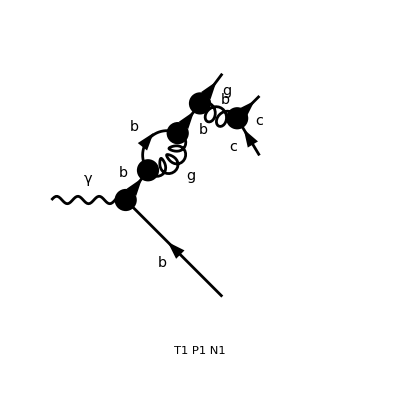

Amplitude after Fire (without PreFactor):

(4 e IntF(1/(r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])),k1) (-8 r^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2+16 r OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2-8 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2+8 r^2 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2-16 r (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+8 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+16 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-40 r^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+32 r (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-8 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+8 r^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2-16 r (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2+8 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2-4 r s OverBar[p4]^Bc1 (ḡ)^Bc2γ-4 r^2 s (ḡ)^Bc1γ OverBar[p3]^Bc2+8 r s (ḡ)^Bc1γ OverBar[p3]^Bc2+12 r^2 s (ḡ)^Bc1Bc2 OverBar[p3]^γ-8 r s (ḡ)^Bc1Bc2 OverBar[p3]^γ+4 r s (ḡ)^Bc1Bc2 OverBar[p4]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+(4 e IntF(1/(OverBar[k1]^2 (r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4]))),k1) (-16 r^4 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^4+64 r^3 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^4-96 r^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^4+64 r OverBar[p4]^Bc1 (ḡ)^Bc2γ m^4-16 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^4+16 r^4 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^4-64 r^3 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^4+96 r^2 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^4-64 r (ḡ)^Bc1γ OverBar[p3]^Bc2 m^4+16 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^4+32 r^5 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4-144 r^4 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4+256 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4-224 r^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4+96 r (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4-16 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^4+16 r^4 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^4-64 r^3 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^4+96 r^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^4-64 r (ḡ)^Bc1Bc2 OverBar[p4]^γ m^4+16 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^4-16 r^3 s OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2+32 r^2 s OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2-16 r s OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2-8 r^4 s (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+40 r^3 s (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2-56 r^2 s (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+24 r s (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+40 r^4 s (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-104 r^3 s (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+88 r^2 s (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-24 r s (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+16 r^3 s (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2-32 r^2 s (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2+16 r s (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2+4 r^2 s^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ-12 r^3 s^2 (ḡ)^Bc1γ OverBar[p3]^Bc2+8 r^2 s^2 (ḡ)^Bc1γ OverBar[p3]^Bc2+4 r^3 s^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ-8 r^2 s^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ-4 r^2 s^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+ϵ ((4 e IntF(1/(r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])),k1) (8 r^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2-16 r OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2+8 OverBar[p4]^Bc1 (ḡ)^Bc2γ m^2-8 r^2 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2+16 r (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2-8 (ḡ)^Bc1γ OverBar[p3]^Bc2 m^2-16 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+40 r^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-32 r (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2+8 (ḡ)^Bc1Bc2 OverBar[p3]^γ m^2-8 r^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2+16 r (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2-8 (ḡ)^Bc1Bc2 OverBar[p4]^γ m^2+4 r^2 s OverBar[p4]^Bc1 (ḡ)^Bc2γ+8 r^2 s (ḡ)^Bc1γ OverBar[p3]^Bc2-12 r s (ḡ)^Bc1γ OverBar[p3]^Bc2-8 r^3 s (ḡ)^Bc1Bc2 OverBar[p3]^γ+4 r s (ḡ)^Bc1Bc2 OverBar[p3]^γ+16 r^3 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ-32 r^2 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ+16 r OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ-4 r^2 s (ḡ)^Bc1Bc2 OverBar[p4]^γ-(4 r^2 s^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ)/m^2+(8 r^2 s OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ)/m^2) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+(4 e IntF(1/(OverBar[k1]^2 (r s+OverBar[k1]^2-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4]))),k1) ((4 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ s^3)/m^2+12 r^3 OverBar[p4]^Bc1 (ḡ)^Bc2γ s^2-16 r^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ s^2+16 r^3 (ḡ)^Bc1γ OverBar[p3]^Bc2 s^2-12 r^2 (ḡ)^Bc1γ OverBar[p3]^Bc2 s^2-16 r^4 (ḡ)^Bc1Bc2 OverBar[p3]^γ s^2+24 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ s^2-4 r^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ s^2-(8 r^3 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ s^2)/m^2-12 r^3 (ḡ)^Bc1Bc2 OverBar[p4]^γ s^2+16 r^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ s^2+8 m^2 r^4 OverBar[p4]^Bc1 (ḡ)^Bc2γ s-24 m^2 r^3 OverBar[p4]^Bc1 (ḡ)^Bc2γ s+24 m^2 r^2 OverBar[p4]^Bc1 (ḡ)^Bc2γ s-8 m^2 r OverBar[p4]^Bc1 (ḡ)^Bc2γ s+8 m^2 r^4 (ḡ)^Bc1γ OverBar[p3]^Bc2 s-24 m^2 r^3 (ḡ)^Bc1γ OverBar[p3]^Bc2 s+24 m^2 r^2 (ḡ)^Bc1γ OverBar[p3]^Bc2 s-8 m^2 r (ḡ)^Bc1γ OverBar[p3]^Bc2 s-16 m^2 r^5 (ḡ)^Bc1Bc2 OverBar[p3]^γ s+56 m^2 r^4 (ḡ)^Bc1Bc2 OverBar[p3]^γ s-72 m^2 r^3 (ḡ)^Bc1Bc2 OverBar[p3]^γ s+40 m^2 r^2 (ḡ)^Bc1Bc2 OverBar[p3]^γ s-8 m^2 r (ḡ)^Bc1Bc2 OverBar[p3]^γ s+32 r^4 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ s-64 r^3 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ s+32 r^2 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ s-8 m^2 r^4 (ḡ)^Bc1Bc2 OverBar[p4]^γ s+24 m^2 r^3 (ḡ)^Bc1Bc2 OverBar[p4]^γ s-24 m^2 r^2 (ḡ)^Bc1Bc2 OverBar[p4]^γ s+8 m^2 r (ḡ)^Bc1Bc2 OverBar[p4]^γ s+32 m^2 r^5 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ-128 m^2 r^4 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ+192 m^2 r^3 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ-128 m^2 r^2 OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ+32 m^2 r OverBar[p4]^Bc1 OverBar[p3]^Bc2 OverBar[p3]^γ) g_s^4)/(27 r^4 s^3 (r (s/m^2-2)+r^2+1)))

```mathematica
MyDiagrPlot[86]
```